```mathematica
FabiusF::usage = "FabiusF[x] gives the value of the Fabius function F(x) for a non-negative real argument x.";
Macros`SetArgumentCount[FabiusF, 1];
SyntaxInformation[FabiusF] = {"ArgumentsPattern" -> {_}};
SetAttributes[FabiusF, {NumericFunction, Listable}];

Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &

(*https://mathematica.stackexchange.com/a/13245*)
powerOfTwoQ[n_] := IntegerQ[n] && BitAnd[n, n - 1] == 0

FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[0 <= Re[x] && Im[x] == 0, powerOfTwoQ[Denominator[x]], Message[FabiusF::realnn, x]; False] := iFabiusF[x]

ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);

tri[x_] := Piecewise[{{2 - x, x > 1}}, x]

iFabiusF[x_] := Module[{prec = Precision[x], s = 1, y = 0, z = SetPrecision[x, Infinity], n, p, q, tol, w}, z = If[0 <= z <= 2, tri[z], q = Quotient[z, 2];
        (*can replace ThueMorse[] with the implementation in https://mathematica.stackexchange.com/a/89351*)If[ThueMorse[q] == 1, s = -1]; tri[z - 2 q]];
    tol = 10^(-prec);
    While[z > 0, n = -Floor[RealExponent[z, 2]]; p = 2^n; z -= 1/p; w = 1;
      Do[w = ariasD[m] + p z w/(n - m + 1); p /= 2, {m, n}];
      y = w - y;
      If[Abs[w] < Abs[y] tol, Break[]]];
    SetPrecision[s Abs[y], prec]]
```

```mathematica
ClearAll[iCurvaturePlotHelper,CurvaturePlot]
iCurvaturePlotHelper[f_?(Head[#]=!=List&),{t_,tmin_,tmax_},{{x0_,y0_},θ0_},opts:OptionsPattern[]]:=Module[{sol,θ,x,y,if},
sol=NDSolve[{
θ'[t]==f,
x'[t]==Cos[θ[t]],
y'[t]==Sin[θ[t]],
θ[tmin]==θ0,
x[tmin]==x0,
y[tmin]==y0
},{x,y},{t,tmin,tmax},opts];
if={x[#],y[#]}&/.First[sol];
if
]
CurvaturePlot[f_,{t_,tmin_,tmax_},opts:OptionsPattern[]]:=CurvaturePlot[f,{t,tmin,tmax},{{0,0},0},opts]
CurvaturePlot[f_,{t_,tmin_,tmax_},p:{{x0_,y0_},θ0_},opts:OptionsPattern[]]:=Module[{θ,x,y,sol,rlsplot,rlsndsolve,if,ifs},
rlsplot=FilterRules[{opts},Options[ParametricPlot]];
rlsndsolve=FilterRules[{opts},Options[NDSolve]];
If[Head[f]===List,
ifs=iCurvaturePlotHelper[#,{t,tmin,tmax},p,Evaluate@(Sequence@@rlsndsolve)]&/@f;
ParametricPlot[Evaluate[#[tplot]&/@ifs],{tplot,tmin,tmax},Evaluate@(Sequence@@rlsplot)]
,
if=iCurvaturePlotHelper[f,{t,tmin,tmax},p,Evaluate@(Sequence@@rlsndsolve)];
ParametricPlot[Evaluate[if[tplot]],{tplot,tmin,tmax},Evaluate@(Sequence@@rlsplot)]
]
]
```

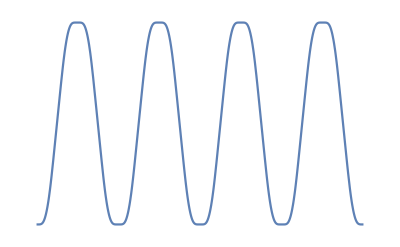
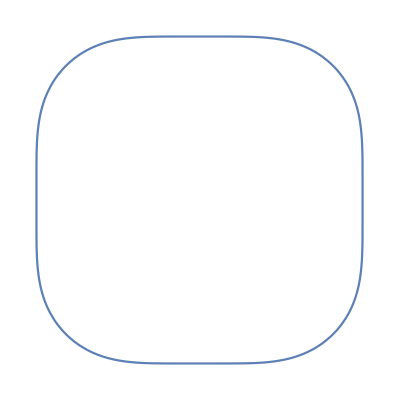

```mathematica
{
Plot[Piecewise[{{Abs[FabiusF[x/Pi*2]],x<2},{Abs[FabiusF[x/Pi*2]],x>2}}],{x,0,4*Pi},Axes->False]
,
CurvaturePlot[Piecewise[{{Abs[FabiusF[x/Pi*2]],x<2},{Abs[FabiusF[x/Pi*2]],x>2}}],{x,0,4*Pi},Axes->False]
}
```

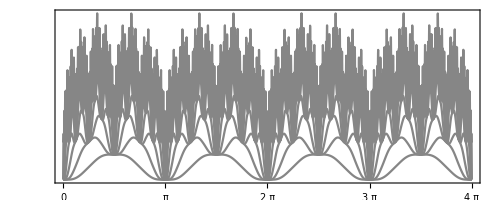

```mathematica
Show[
Plot[Abs[FabiusF[x/Pi*2]]*(1/2^4),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/2^4))+Abs[FabiusF'[x/Pi*2]]*(1/2^5),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/2^4))+Abs[FabiusF'[x/Pi*2]]*(1/2^5)+Abs[FabiusF''[x/Pi*2]]*(1/2^7),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/2^4))+Abs[FabiusF'[x/Pi*2]]*(1/2^5)+Abs[FabiusF''[x/Pi*2]]*(1/2^7)+Abs[FabiusF'''[x/Pi*2]]*(1/2^10),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/2^4))+Abs[FabiusF'[x/Pi*2]]*(1/2^5)+Abs[FabiusF''[x/Pi*2]]*(1/2^7)+Abs[FabiusF'''[x/Pi*2]]*(1/2^10)+Abs[FabiusF''''[x/Pi*2]]*(1/2^14),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/2^4))+Abs[FabiusF'[x/Pi*2]]*(1/2^5)+Abs[FabiusF''[x/Pi*2]]*(1/2^7)+Abs[FabiusF'''[x/Pi*2]]*(1/2^10)+Abs[FabiusF''''[x/Pi*2]]*(1/2^14)+Abs[FabiusF'''''[x/Pi*2]]*(1/2^19),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/2^4))+Abs[FabiusF'[x/Pi*2]]*(1/2^5)+Abs[FabiusF''[x/Pi*2]]*(1/2^7)+Abs[FabiusF'''[x/Pi*2]]*(1/2^10)+Abs[FabiusF''''[x/Pi*2]]*(1/2^14)+Abs[FabiusF'''''[x/Pi*2]]*(1/2^19)+Abs[FabiusF''''''[x/Pi*2]]*(1/2^25),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/2^4))+Abs[FabiusF'[x/Pi*2]]*(1/2^5)+Abs[FabiusF''[x/Pi*2]]*(1/2^7)+Abs[FabiusF'''[x/Pi*2]]*(1/2^10)+Abs[FabiusF''''[x/Pi*2]]*(1/2^14)+Abs[FabiusF'''''[x/Pi*2]]*(1/2^19)+Abs[FabiusF''''''[x/Pi*2]]*(1/2^25)+Abs[FabiusF'''''''[x/Pi*2]]*(1/2^32),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True]
,
PlotRange->Full,FrameTicks->{{0,1*π/2,2*π/2,3*π/2,4*π/2,5*π/2,6*π/2,7*π/2,8*π/2},{1}},ImageSize->Full,PlotStyle->GrayLevel[135/256],FrameStyle->GrayLevel[172/256],Frame->True
]
```

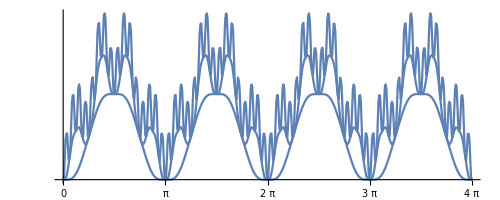

```mathematica
Show[
Plot[Abs[FabiusF[x/Pi*2]]*(1/8),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/8))+Abs[FabiusF''[x/Pi*2]]*(1/2^7),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full]
,
Plot[(Abs[FabiusF[x/Pi*2]]*(1/8))+Abs[FabiusF''[x/Pi*2]]*(1/2^7)+Abs[FabiusF''''[x/Pi*2]]*(1/2^14),{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^12,ImageSize->Full]

,
PlotRange->Full,Ticks->{{0,1*π/2,2*π/2,3*π/2,4*π/2,5*π/2,6*π/2,7*π/2,8*π/2},{1},ImageSize->Full}
]
```

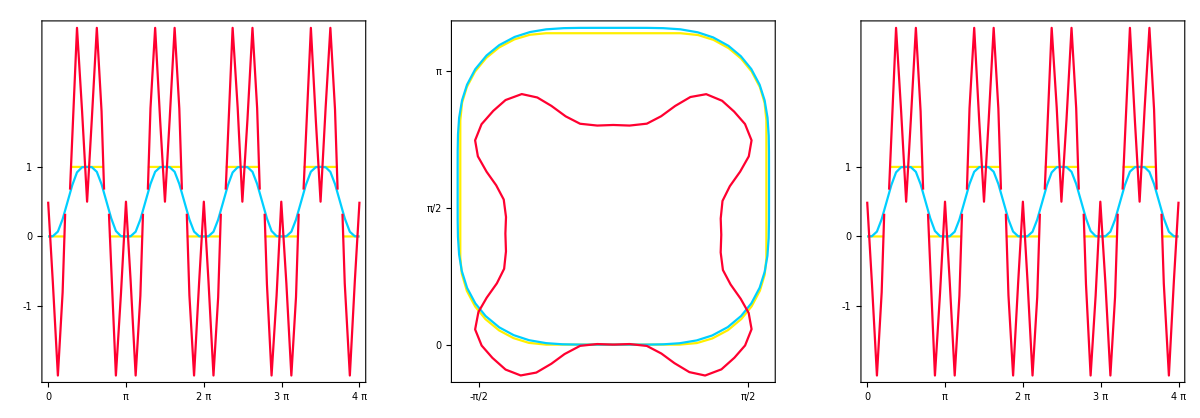

```mathematica
OOOO=Round[SawtoothWave[(x+Pi/4)/Pi]];
OOOOOOOO=Abs[FabiusF[x/Pi*2]];
OOOO8888OOOO=.5-((Abs[FabiusF[(x+0)/Pi*8]]*(1/2^-4))+(2*Abs[FabiusF'[(x+0)/Pi*4]])*(1/2^-4))*(Round[SawtoothWave[(x-Pi/4)/Pi*1]]*1-.5)/16;

⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪=Plot[{OOOO,OOOOOOOO,OOOO8888OOOO},{x,0,4*Pi},Axes->True,PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^6,ImageSize->Automatic,Frame->True,FrameTicks->{{0,1*π/2,2*π/2,3*π/2,4*π/2,5*π/2,6*π/2,7*π/2,8*π/2},{-1,0,1}},PlotStyle->{Hue[2.5/16,1,1],Hue[8.5/16,1,1],Hue[15.5/16,1,1]}];

⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◯⚪ᗱᗴ⚪ᴥ⚪ᑎ⚪✤⚪ᗩ⚪ᗯ⚪ᴥ⚪ᑎ⚪ᑐᑕ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ᑐᑕ⚪ᑎ⚪ᴥ⚪ᗯ⚪ᗩ⚪✤⚪ᑎ⚪ᴥ⚪ᗱᗴ⚪◯⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪=CurvaturePlot[{OOOO,OOOOOOOO,OOOO8888OOOO},{x,0,4*Pi},Axes->{True,True},PlotRange->Full,AspectRatio->Automatic,MaxRecursion->0,PlotPoints->1+2^6,ImageSize->Large,Frame->True,FrameTicks->{{-1*π/2,0,1*π/2,2*π/2,3*π/2,4*π/2,5*π/2,6*π/2,7*π/2,8*π/2},{-1*π/2,0,1*π/2,2*π/2,3*π/2,4*π/2,5*π/2,6*π/2,7*π/2,8*π/2}},PlotStyle->{Hue[2.5/16,1,1],Hue[8.5/16,1,1],Hue[15.5/16,1,1]}];

GraphicsGrid[
{
{
⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪
,
⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◯⚪ᗱᗴ⚪ᴥ⚪ᑎ⚪✤⚪ᗩ⚪ᗯ⚪ᴥ⚪ᑎ⚪ᑐᑕ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ᑐᑕ⚪ᑎ⚪ᴥ⚪ᗯ⚪ᗩ⚪✤⚪ᑎ⚪ᴥ⚪ᗱᗴ⚪◯⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪
,
⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪
}
}
,
ImageSize->Full
]
```

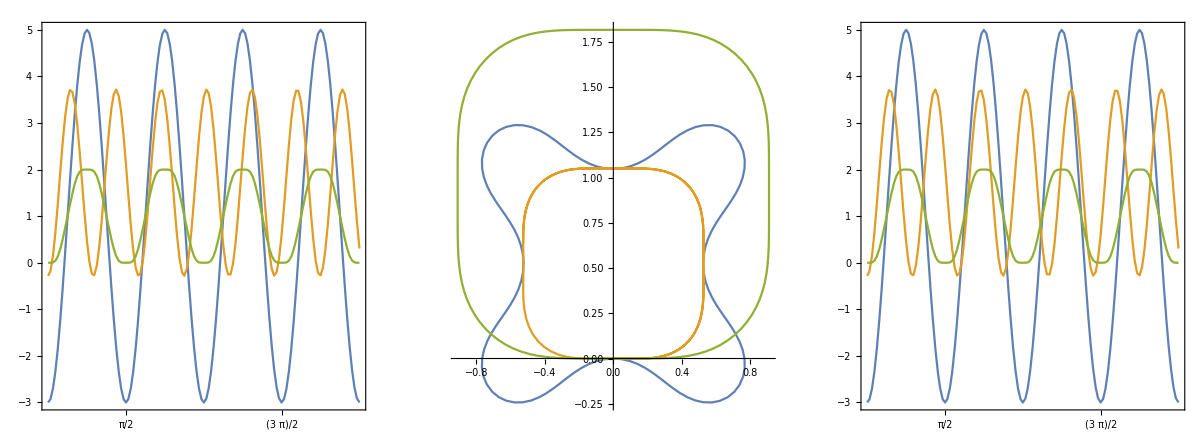

```mathematica
O8O8O=1-4*Cos[4*x];
OO88OO88OO=1.71875-2*Cos[6.875*x];
(*OO88OO88OO=(-1+(8*(Abs[FabiusF[x/Pi*4]])/2));*)
O8O8O8O8O=1*(0+(1*(Abs[FabiusF[x/Pi*4]])*2));
GraphicsGrid[
{{
Plot[{O8O8O,OO88OO88OO,O8O8O8O8O},{x,0,2*Pi},MaxRecursion->0,PlotPoints->1+2^7,AspectRatio->Pi/16,ImageSize->Automatic,Frame->True,FrameTicks->{{-1*π/2,0,1*π/2,2*π/2,3*π/2,4*π/2,5*π/2,6*π/2,7*π/2,8*π/2},Automatic}]
,
CurvaturePlot[{O8O8O,OO88OO88OO,O8O8O8O8O},{x,0,2*Pi},MaxRecursion->0,PlotPoints->1+2^7,ImageSize->Full]
,
Plot[{O8O8O,OO88OO88OO,O8O8O8O8O},{x,0,2*Pi},MaxRecursion->0,PlotPoints->1+2^7,AspectRatio->Pi/16,ImageSize->Automatic,Frame->True,FrameTicks->{{-1*π/2,0,1*π/2,2*π/2,3*π/2,4*π/2,5*π/2,6*π/2,7*π/2,8*π/2},Automatic}]
}}
,
ImageSize->Full
]
```